```mathematica
Morig = {{0,I*J,I*(-α+ϵ),-I*J,0,0,-I*(-α+ϵ),0,0},{I*J,-Γ,I*(-α+ϵ),0,-I*J,0,0,-I*(-α+ϵ),0},{I*(-α+ϵ),I*(-α+ϵ),-Γ,0,0,-I*J,0,0,-I*(-α+ϵ)},{-I*J,0,0,-Γ,I*J,I*(-α+ϵ),-I*(-α+ϵ),0,0},{0,-I*J,0,I*J,0,I*(-α+ϵ),0,-I*(-α+ϵ),0},{0,0,-I*J,I*(-α+ϵ),I*(-α+ϵ),-Γ,0,0,-I*(-α+ϵ)},{-I*(-α+ϵ),0,0,-I*(-α+ϵ),0,0,-Γ,I*J,I*(-α+ϵ)},{0,-I*(-α+ϵ),0,0,-I*(-α+ϵ),0,I*J,-Γ,I*(-α+ϵ)},{0,0,-I*(-α+ϵ),0,0,-I*(-α+ϵ),I*(-α+ϵ),I*(-α+ϵ),0}};
Morig //TableForm
```

0 | ⅈ J | ⅈ (-α+ϵ) | -ⅈ J | 0 | 0 | -ⅈ (-α+ϵ) | 0 | 0
ⅈ J | -Γ | ⅈ (-α+ϵ) | 0 | -ⅈ J | 0 | 0 | -ⅈ (-α+ϵ) | 0
ⅈ (-α+ϵ) | ⅈ (-α+ϵ) | -Γ | 0 | 0 | -ⅈ J | 0 | 0 | -ⅈ (-α+ϵ)
-ⅈ J | 0 | 0 | -Γ | ⅈ J | ⅈ (-α+ϵ) | -ⅈ (-α+ϵ) | 0 | 0
0 | -ⅈ J | 0 | ⅈ J | 0 | ⅈ (-α+ϵ) | 0 | -ⅈ (-α+ϵ) | 0
0 | 0 | -ⅈ J | ⅈ (-α+ϵ) | ⅈ (-α+ϵ) | -Γ | 0 | 0 | -ⅈ (-α+ϵ)
-ⅈ (-α+ϵ) | 0 | 0 | -ⅈ (-α+ϵ) | 0 | 0 | -Γ | ⅈ J | ⅈ (-α+ϵ)
0 | -ⅈ (-α+ϵ) | 0 | 0 | -ⅈ (-α+ϵ) | 0 | ⅈ J | -Γ | ⅈ (-α+ϵ)
0 | 0 | -ⅈ (-α+ϵ) | 0 | 0 | -ⅈ (-α+ϵ) | ⅈ (-α+ϵ) | ⅈ (-α+ϵ) | 0

```mathematica
M = Morig /. {Γ->10^(-1),  ϵ->10^(-4), J->0.1}
```

{{0,0.+0.1 ⅈ,ⅈ (1/10000-α),0.-0.1 ⅈ,0,0,-ⅈ (1/10000-α),0,0},{0.+0.1 ⅈ,-1/10,ⅈ (1/10000-α),0,0.-0.1 ⅈ,0,0,-ⅈ (1/10000-α),0},{ⅈ (1/10000-α),ⅈ (1/10000-α),-1/10,0,0,0.-0.1 ⅈ,0,0,-ⅈ (1/10000-α)},{0.-0.1 ⅈ,0,0,-1/10,0.+0.1 ⅈ,ⅈ (1/10000-α),-ⅈ (1/10000-α),0,0},{0,0.-0.1 ⅈ,0,0.+0.1 ⅈ,0,ⅈ (1/10000-α),0,-ⅈ (1/10000-α),0},{0,0,0.-0.1 ⅈ,ⅈ (1/10000-α),ⅈ (1/10000-α),-1/10,0,0,-ⅈ (1/10000-α)},{-ⅈ (1/10000-α),0,0,-ⅈ (1/10000-α),0,0,-1/10,0.+0.1 ⅈ,ⅈ (1/10000-α)},{0,-ⅈ (1/10000-α),0,0,-ⅈ (1/10000-α),0,0.+0.1 ⅈ,-1/10,ⅈ (1/10000-α)},{0,0,-ⅈ (1/10000-α),0,0,-ⅈ (1/10000-α),ⅈ (1/10000-α),ⅈ (1/10000-α),0}}

```mathematica
(* =========================================*)(*Parameters*)(* =========================================*)
epsilonStart = 10^(-6);
epsilonStop=100;
step=1.01;

outfile=FileNameJoin[{NotebookDirectory[],"gamma=1e-1; J=0.1; epsilon=1e-4.dat"}];


(* =========================================*)
(*Generate epsilon values*)
(* =========================================*)

epsList=PowerRange[epsilonStart,epsilonStop,step];

(*Number of eigenvalues*)
nEvals=Length[Eigenvalues[M/. α->First[epsList]]];

(* =========================================*)
(*Build data table*)
(* =========================================*)

data=Table[Module[{ev},ev=Sort[N[Eigenvalues[N[M /. α -> eps]]]];
Join[{N[eps]},Flatten[{Re[#], Im[#]}&/@ev]]],{eps,epsList}];


(* =========================================*)
(*Export*)
(* =========================================*)

Export[outfile,data,"Table"];

Print["Saved ",Length[data]," rows to ",outfile];
```

Saved 1852 rows to /nfs/cptg/u4/kratzel/Documents/Wolfram Mathematica/[3.0] [three-site (degenerate), single-body, general epsilon's, local dephasing] [june 5]/[3.0.3] [evals of delta case] [july 6]/gamma=1e-1; J=0.1; epsilon=1e-4.dat

$Aborted

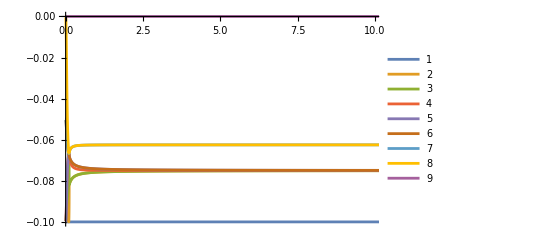

```mathematica
ListLinePlot[data[[All,{1,#}]]&/@Range[2,Length[data[[1]]],2],PlotLegends->Automatic]
```